```mathematica
Clear[tp]
lst={};
pow = 4;
For[n=1,n≤10^pow,n++,
tp=Intersection[Sign[Differences[IntegerDigits[n]]]];
If[tp=={-1,0}||tp=={0}||tp=={0,1}||tp=={1}||tp=={-1},lst=Append[lst,n]];
];
```

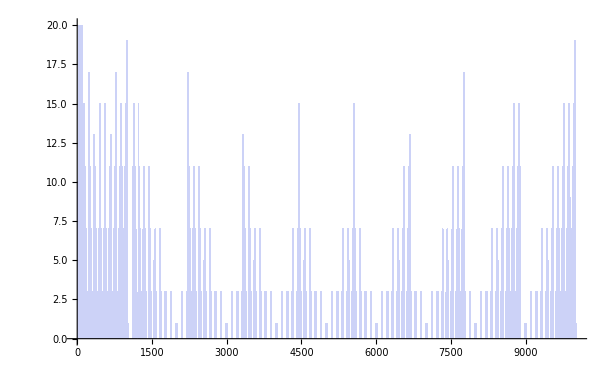

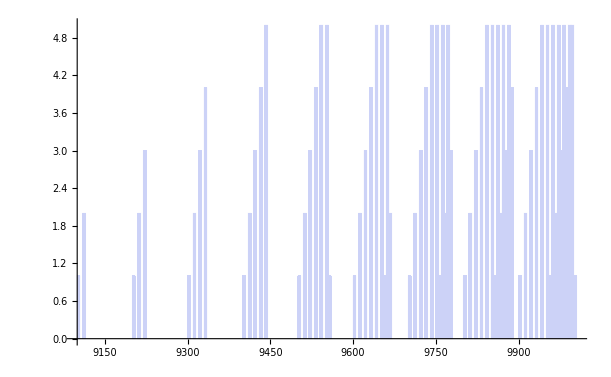

220

```mathematica
Histogram[lst,500]
Histogram[Select[lst,#>10^pow-10^(pow-1)&],200]
Length[Select[lst,#>10^pow-10^(pow-1)&]]
```

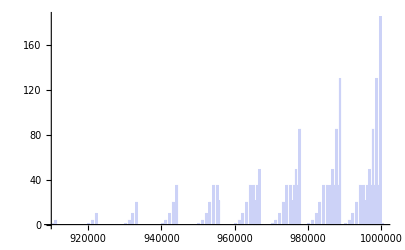

2002